Demo file of d=2, p=3 and p=7
 investigating relation of norm equivalances
 to the Hopf Map, this time including zero norm:
   Hanson - 26 June 2015

### Utilities:

```mathematica
Needs["CCompilerDriver`"]
Needs["CompiledFunctionTools`"]
$CompilationTarget="WVM"(*If[CCompilers[]≠{},"C","WVM"]*)
On[ Compile::noinfo];
<<CompiledFunctionTools`
```

WVM

#### Utility Library

```mathematica
cConj=Compile[{{q,_Integer,1}},{q⟦1⟧,-q⟦2⟧},RuntimeAttributes->Listable,CompilationOptions->{"InlineExternalDefinitions"->True},RuntimeOptions->"Speed"];
```

```mathematica
cMod=Compile[{{z,_Integer},{p,_Integer}},Mod[z,p,Quotient[1-p,2]],RuntimeAttributes->Listable,CompilationOptions->{"InlineExternalDefinitions"->True},RuntimeOptions->"Speed"];
```

```mathematica
cTimes=Compile[{{q,_Integer,1},{r,_Integer,1}},{q⟦1⟧r⟦1⟧-q⟦2⟧r⟦2⟧,q⟦1⟧r⟦2⟧+q⟦2⟧r⟦1⟧},RuntimeAttributes->Listable,CompilationOptions->{"InlineExternalDefinitions"->True},RuntimeOptions->"Speed"];
cTimes[{1,0},{1,0}]
```

{1,0}

```mathematica
cTimesVec=Compile[{{q,_Integer,1},{vec,_Integer,2},{p,_Integer}},Module[{x1=q⟦1⟧,y1=q⟦2⟧,x2,y2},
Table[{x2,y2}=vec⟦i⟧;{cMod[x1 x2-y1 y2,p], cMod[x2 y1+x1 y2,p]},{i,Length[vec]}]],
CompilationOptions->{"InlineExternalDefinitions"->True},RuntimeOptions->"Speed"];
```

```mathematica
cNorm2[vec_List,p_Integer]:=cNorm2[vec,p]=Module[{cConjvec=cConj[vec]},
cMod[∑_(j=1)^Length[vec] (vec⟦j,1⟧cConjvec⟦j,1⟧-vec⟦j,2⟧cConjvec⟦j,2⟧),p]]
```

```mathematica
legalPs=Select[Prime[Range[27]],Divisible[#-3,4]&]
```

{3,7,11,19,23,31,43,47,59,67,71,79,83,103}

```mathematica
rBasis[p_] := First/@Tuples[Range[-((p-1)/2),(p-1)/2],1]
```

```mathematica
(* Remove origin *)rBasisZ[p_]:=Complement[First/@Tuples[Range[Quotient[1-p,2],Quotient[p-1,2]],1], {0}]
```

```mathematica
cBasis=Compile[{{p,_Integer}},Flatten[Table[{s,t},{s,Quotient[1-p,2],Quotient[p-1,2]},{t,Quotient[1-p,2],Quotient[p-1,2]}],1],RuntimeAttributes->Listable,Parallelization->True,CompilationOptions->{"InlineExternalDefinitions"->True},RuntimeOptions->"Speed"];
cBasis[3]
```

{{-1,-1},{-1,0},{-1,1},{0,-1},{0,0},{0,1},{1,-1},{1,0},{1,1}}

```mathematica
(* Remove origin *)cBasisZ[p_Integer]:=cBasisZ[p]=Complement[cBasis[p], {{0,0}}]
```

```mathematica
rMod[r_,p_]:= Mod[r,p,(1-p)/2]
```

```mathematica
cConjAbstract[{x_,y_},p_] := cPow[{x,y},p,p]
```

```mathematica
cQuotientRemainder=Compile[{{α,_Integer,1},{β,_Integer,1}},Module[{a=α⟦1⟧,b=α⟦2⟧,c=β⟦1⟧,d=β⟦2⟧,p=0,q=0},p=Round[(a c+b d)/(c^2+d^2)];q=Round[(b c-a d)/(c^2+d^2)];{{p,q},α-{p c-q d,p d+q c}}],
RuntimeAttributes->Listable,CompilationOptions->{"InlineExternalDefinitions"->True},RuntimeOptions->"Speed"];
cQuotientRemainder[{3,0},{1,1}]
```

{{2,-2},{-1,0}}

```mathematica
cInverse[{x_Integer,y_Integer},p_Integer]:=cInverse[{x,y},p] =cPow[{x,y},p^2-2,p]
(*cInverse=Compile[{{q,_Integer,1},{p,_Integer}},
(*Let q^-1 be the inverse of q in Subscript[𝔽, p^2]. Then if we think q and q^-1 as Gaussian integers ℤ[ⅈ], there is s such that q^-1×q+s×p==1, and 1 is the greatest common divisor for p and q in ℤ[ⅈ]. Therefore, we can use the greatest common divisor algorithm to compute the inverse.*)
Module[{}ExtendedGCD[q⟦1⟧+ⅈ q⟦2⟧,p],RuntimeAttributes->Listable,CompilationOptions->{"InlineExternalDefinitions"->True},RuntimeOptions->"Speed"];*)
cInverse[{1,1},3]
```

{-1,1}

```mathematica
cPow[{x_Integer,y_Integer},power_Integer,p_Integer]:=cPow[{x,y},power,p]=Module[{z=(x+I y)^power,re,im},
re=ComplexExpand[Re[z]];im=ComplexExpand[Im[z]];
{Mod[re,p,(1-p)/2], Mod[im,p,(1-p)/2]}]
```

When you need to see if square root, or nth root, exists in field:

```mathematica
findRoot[value_,p_] := (* Square Root *)
Module[{base=p^2-1,basis=cBasisZ[p],
val=cMod[value,p], (* Validity check *)
test,out={}},
Do[test=basis[[k]];If[cMod[cTimes[test,test],p]==val,AppendTo[out, test]],
{k,1,base}];out ]
```

```mathematica
findNthRoot[value_List,n_Integer,p_Integer]:= Module[{size=p^2-1,basis=cBasisZ[p],val=cMod[value,p], (* Validity check *),
out={},test},
Do[test=basis⟦k⟧;If[cPow[test,n,p] ==val,AppendTo[out,test]],{k,1,size}];
out]
```

```mathematica
findANthRoot[value_List,n_Integer,p_Integer]:= findANthRoot[value,n,p]=Module[{val=cMod[value,p](* Validity check *)},
Do[If[cPow[test,n,p] ==val,Return[test]],{test,cBasisZ[p]}]]
findANthRoot[{0,-1},2,3]
```

{-1,-1}

```mathematica
findInverseNorm[value_List,p_Integer]:=(*findInverseNorm[value,p]=*)
Module[{modValue=cMod[value,p],inverseNorm},If[modValue=={0,0}∨modValue⟦2⟧≠0,{},inverseNorm=cInverse[modValue,p];Do[If[cMod[cTimes[cConj[i],i],p]==inverseNorm,Return[i]],{i,Join[{{0,0},{1,0}},Complement[cBasis[p],{{0,0},{1,0}}]]}]]]
findInverseNorm[{0,-1},3]
Table[Module[{b=findInverseNorm[{cNorm2[{value},3],0},3]},If[b=={},{},cNorm2[{cTimes[b,value]},3]]],{value,cBasis[3]}]
```

{}

{1,1,1,1,{},1,1,1,1}

Collection of equivalence-map  forms

```mathematica
genDVectors[d_,p_]:=Module[{basis=cBasis[p]},
Complement[Tuples[basis,d],
(* LIST *) {Array[{0,0}&,d]}]]
```

```mathematica
mapToCanonical[vec_List,p_Integer]:=mapToCanonical[vec,p]=Module[{
index=Position[vec,Except[{0,0}],{1},Heads->False],div},
If[index=={},vec,
index=index⟦1,1⟧;
div=cInverse[vec⟦index⟧,p];
Join[ConstantArray[{0,0},index-1],{{1,0}},Table[cMod[cTimes[div,vec⟦k⟧],p],{k,index+1,Length[vec]}]]]]
mapToCanonical[{{-1,-1},{1,1}},3]
```

{{1,0},{-1,0}}

```mathematica
chooseAllNormClasses[vectorList_List,p_Integer]:=
Module[{d=Length[vectorList⟦1⟧],equivs = Union@(mapToCanonical[#,p]&/@vectorList),normalized},
normalized=GatherBy[equivs,cNorm2[#,p]&];
SortBy[normalized,Abs[cNorm2[#⟦1⟧,p]]&]]
```

#### Selection Utilities: Note that it WILL NOT work to try to divide by the norm, because it can be a complex root, and the complex conjugation in cNorm2 will mess up the division...

```mathematica
mapCanonToUnit[vec_List,p_Integer]:=mapCanonToUnit[vec,p]=Module[{normsq=cNorm2[vec,p]},If[normsq==0,False,cTimesVec[findInverseNorm[{normsq,0},p],vec,p]]]
```

```mathematica
pruneCanonicalToUnit[canonList_,p_]:=Module[{removedNull},
removedNull = Select[canonList,If[cNorm2[#,p]==0,False,True,True]&];
Map[mapCanonToUnit[#,p]&,removedNull]]
```

#### Split up the Hopf with and without radius=1 scaling.

```mathematica
hopf3[{x0_,y0_},{x1_,y1_},p_] :=
Map[rMod[#,p]&,{2 (x0 x1+y0 y1),2 (x1 y0-x0 y1),x0^2+y0^2-(x1^2+y1^2)} ]
```

hopfPart: Usage: need  two-vectors with x+ Iy as {x,y}:
      vec3list = Map[hopf3[#[[1]], #[[2]], p]&, {2-vector in Fp^2}]

```mathematica
hopfPart[vec3List_,colorL_:Blue,colorP_:Red,norm1P_:False]:=Module[{vectors = If[norm1P,Map[Normalize,vec3List],vec3List]},Graphics3D[{colorL,Thickness[0.010],Map[Line[{{0,0,0},#}]&,vectors],
colorP,PointSize[0.04],Point[vectors]},Axes->True,AxesLabel->{"X","Y","Z"}] ]
```

### Data and investigations:

```mathematica
(* genDvectors *) Select[Tuples[cBasis[3],2],(#≠ {{0,0},{0,0}})&];
```

```mathematica
d2p31qbit=genDVectors[2,3];
```

```mathematica
Map[cNorm2[#,3]&,d2p31qbit]
```

{1,0,1,0,-1,0,1,0,1,0,-1,0,-1,1,-1,0,-1,0,1,0,1,0,-1,0,1,0,1,0,-1,0,-1,1,-1,0,-1,0,-1,1,-1,1,1,-1,1,-1,0,-1,0,-1,1,-1,0,-1,0,1,0,1,0,-1,0,1,0,1,0,-1,0,-1,1,-1,0,-1,0,1,0,1,0,-1,0,1,0,1}

```mathematica
{d2p31qbit//Length,"  Tally of norms:",Tally[%]}
```

{80,  Tally of norms:,{{1,24},{0,32},{-1,24}}}

```mathematica
d2p71qbit=genDVectors[2,7];
```

```mathematica
Map[cNorm2[#,3]&,d2p71qbit];
```

```mathematica
{d2p71qbit//Length,"  Tally of norms:",Tally[%]}
```

{2400,  Tally of norms:,{{0,848},{1,688},{-1,864}}}

Note that zero-norm is special in the full 80-element list,
   while unit-norm is special after equivalencing.

Split out the zero-norms FIRST to make it easy to
   break them apart; then later, we reinsert them in the
   middle at the right place when appropriate in the Hopf map.

```mathematica
test23=chooseAllNormClasses[genDVectors[2,3],3]
```

{{{{1,0},{-1,-1}},{{1,0},{-1,1}},{{1,0},{1,-1}},{{1,0},{1,1}}},{{{0,0},{1,0}},{{1,0},{0,0}}},{{{1,0},{-1,0}},{{1,0},{0,-1}},{{1,0},{0,1}},{{1,0},{1,0}}}}

```mathematica
Dimensions/@test23
```

{{4,2,2},{2,2,2},{4,2,2}}

```mathematica
Map[cNorm2[#,3]&,test23,{2}]
```

{{0,0,0,0},{1,1},{-1,-1,-1,-1}}

```mathematica
test27=chooseAllNormClasses[genDVectors[2,7],7]
```

{{{{1,0},{-3,-2}},{{1,0},{-3,2}},{{1,0},{-2,-3}},{{1,0},{-2,3}},{{1,0},{2,-3}},{{1,0},{2,3}},{{1,0},{3,-2}},{{1,0},{3,2}}},{{{0,0},{1,0}},{{1,0},{0,0}}},{{{1,0},{-2,-1}},{{1,0},{-2,1}},{{1,0},{-1,-2}},{{1,0},{-1,2}},{{1,0},{1,-2}},{{1,0},{1,2}},{{1,0},{2,-1}},{{1,0},{2,1}}},{{{1,0},{-3,-3}},{{1,0},{-3,3}},{{1,0},{-2,0}},{{1,0},{0,-2}},{{1,0},{0,2}},{{1,0},{2,0}},{{1,0},{3,-3}},{{1,0},{3,3}}},{{{1,0},{-2,-2}},{{1,0},{-2,2}},{{1,0},{-1,0}},{{1,0},{0,-1}},{{1,0},{0,1}},{{1,0},{1,0}},{{1,0},{2,-2}},{{1,0},{2,2}}},{{{1,0},{-3,-1}},{{1,0},{-3,1}},{{1,0},{-1,-3}},{{1,0},{-1,3}},{{1,0},{1,-3}},{{1,0},{1,3}},{{1,0},{3,-1}},{{1,0},{3,1}}},{{{1,0},{-3,0}},{{1,0},{-1,-1}},{{1,0},{-1,1}},{{1,0},{0,-3}},{{1,0},{0,3}},{{1,0},{1,-1}},{{1,0},{1,1}},{{1,0},{3,0}}}}

```mathematica
Dimensions/@test27
```

{{8,2,2},{2,2,2},{8,2,2},{8,2,2},{8,2,2},{8,2,2},{8,2,2}}

```mathematica
Map[cNorm2[#,7]&,test27,{2}]
```

{{0,0,0,0,0,0,0,0},{1,1},{-1,-1,-1,-1,-1,-1,-1,-1},{-2,-2,-2,-2,-2,-2,-2,-2},{2,2,2,2,2,2,2,2},{-3,-3,-3,-3,-3,-3,-3,-3},{3,3,3,3,3,3,3,3}}

#### d=2, p=3: Now rearrange these in the basis[p] order:

```mathematica
test23raw={test23[[2]],test23[[1]],test23[[3]]}
```

{{{{0,0},{1,0}},{{1,0},{0,0}}},{{{1,0},{-1,-1}},{{1,0},{-1,1}},{{1,0},{1,-1}},{{1,0},{1,1}}},{{{1,0},{-1,0}},{{1,0},{0,-1}},{{1,0},{0,1}},{{1,0},{1,0}}}}

```mathematica
Dimensions/@test23raw
```

{{2,2,2},{4,2,2},{4,2,2}}

```mathematica
Map[cNorm2[#,3]&,test23raw,{2}]
```

{{1,1},{0,0,0,0},{-1,-1,-1,-1}}

```mathematica
test23Normed =Insert[ Map[pruneCanonicalToUnit[#,3]&,Rest@test23],First@test23,2]
```

{{{{0,0},{1,0}},{{1,0},{0,0}}},{{{1,0},{-1,-1}},{{1,0},{-1,1}},{{1,0},{1,-1}},{{1,0},{1,1}}},{{{-1,-1},{1,1}},{{-1,-1},{-1,1}},{{-1,-1},{1,-1}},{{-1,-1},{-1,-1}}}}

```mathematica
Dimensions/@test23Normed
```

{{2,2,2},{4,2,2},{4,2,2}}

```mathematica
Map[cNorm2[#,3]&,test23Normed,{2}]
```

{{1,1},{0,0,0,0},{1,1,1,1}}

EVEN ZERO NORM has a Hopf map...

```mathematica
Map[hopf3[#[[1]],#[[2]],3]&,test23Normed,{2}]
```

{{{0,0,-1},{0,0,1}},{{1,-1,-1},{1,1,-1},{-1,-1,-1},{-1,1,-1}},{{-1,0,0},{0,1,0},{0,-1,0},{1,0,0}}}

Red is zero norm, black is norm one. Norm zero is insensitive
to transforms: group multiplication only changes z=-1 to z=+1.

```mathematica
Show@Table[hopfPart[Map[hopf3[#⟦1⟧,#⟦2⟧,3]&,test23Normed⟦k⟧],Blue,{Cyan,Red,Black}⟦k⟧],{k,3}]
```

-Graphics3D-

#### d=2, p=7: Now rearrange these in the basis[p] order:

```mathematica
test27raw=Join[test27[[2;;4]],{First[test27]},test27[[5;;7]]]
```

{{{{0,0},{1,0}},{{1,0},{0,0}}},{{{1,0},{-2,-1}},{{1,0},{-2,1}},{{1,0},{-1,-2}},{{1,0},{-1,2}},{{1,0},{1,-2}},{{1,0},{1,2}},{{1,0},{2,-1}},{{1,0},{2,1}}},{{{1,0},{-3,-3}},{{1,0},{-3,3}},{{1,0},{-2,0}},{{1,0},{0,-2}},{{1,0},{0,2}},{{1,0},{2,0}},{{1,0},{3,-3}},{{1,0},{3,3}}},{{{1,0},{-3,-2}},{{1,0},{-3,2}},{{1,0},{-2,-3}},{{1,0},{-2,3}},{{1,0},{2,-3}},{{1,0},{2,3}},{{1,0},{3,-2}},{{1,0},{3,2}}},{{{1,0},{-2,-2}},{{1,0},{-2,2}},{{1,0},{-1,0}},{{1,0},{0,-1}},{{1,0},{0,1}},{{1,0},{1,0}},{{1,0},{2,-2}},{{1,0},{2,2}}},{{{1,0},{-3,-1}},{{1,0},{-3,1}},{{1,0},{-1,-3}},{{1,0},{-1,3}},{{1,0},{1,-3}},{{1,0},{1,3}},{{1,0},{3,-1}},{{1,0},{3,1}}},{{{1,0},{-3,0}},{{1,0},{-1,-1}},{{1,0},{-1,1}},{{1,0},{0,-3}},{{1,0},{0,3}},{{1,0},{1,-1}},{{1,0},{1,1}},{{1,0},{3,0}}}}

```mathematica
Dimensions/@test27raw
```

{{2,2,2},{8,2,2},{8,2,2},{8,2,2},{8,2,2},{8,2,2},{8,2,2}}

```mathematica
Map[cNorm2[#,7]&,test27raw,{2}]
```

{{1,1},{-1,-1,-1,-1,-1,-1,-1,-1},{-2,-2,-2,-2,-2,-2,-2,-2},{0,0,0,0,0,0,0,0},{2,2,2,2,2,2,2,2},{-3,-3,-3,-3,-3,-3,-3,-3},{3,3,3,3,3,3,3,3}}

```mathematica
test27Normed =Insert[ Map[pruneCanonicalToUnit[#,7]&,Rest@test27],First@test27,4]
```

{{{{0,0},{1,0}},{{1,0},{0,0}}},{{{-3,-2},{-3,0}},{{-3,-2},{1,1}},{{-3,-2},{-1,1}},{{-3,-2},{0,3}},{{-3,-2},{0,-3}},{{-3,-2},{1,-1}},{{-3,-2},{-1,-1}},{{-3,-2},{3,0}}},{{{-3,-1},{-1,-2}},{{-3,-1},{-2,1}},{{-3,-1},{-1,2}},{{-3,-1},{-2,-1}},{{-3,-1},{2,1}},{{-3,-1},{1,-2}},{{-3,-1},{2,-1}},{{-3,-1},{1,2}}},{{{1,0},{-3,-2}},{{1,0},{-3,2}},{{1,0},{-2,-3}},{{1,0},{-2,3}},{{1,0},{2,-3}},{{1,0},{2,3}},{{1,0},{3,-2}},{{1,0},{3,2}}},{{{-3,-3},{0,-2}},{{-3,-3},{-2,0}},{{-3,-3},{3,3}},{{-3,-3},{-3,3}},{{-3,-3},{3,-3}},{{-3,-3},{-3,-3}},{{-3,-3},{2,0}},{{-3,-3},{0,2}}},{{{-3,0},{2,3}},{{-3,0},{2,-3}},{{-3,0},{3,2}},{{-3,0},{3,-2}},{{-3,0},{-3,2}},{{-3,0},{-3,-2}},{{-3,0},{-2,3}},{{-3,0},{-2,-3}}},{{{-2,-1},{-1,3}},{{-2,-1},{1,3}},{{-2,-1},{3,-1}},{{-2,-1},{-3,-1}},{{-2,-1},{3,1}},{{-2,-1},{-3,1}},{{-2,-1},{-1,-3}},{{-2,-1},{1,-3}}}}

```mathematica
Dimensions/@test27Normed
```

{{2,2,2},{8,2,2},{8,2,2},{8,2,2},{8,2,2},{8,2,2},{8,2,2}}

```mathematica
Map[cNorm2[#,7]&,test27Normed,{2}]
```

{{1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}}

```mathematica
Map[hopf3[#[[1]],#[[2]],7]&,test27Normed,{2}]
```

{{{0,0,-1},{0,0,1}},{{-3,-2,-3},{-3,2,-3},{2,3,-3},{2,-3,-3},{-2,3,-3},{-2,-3,-3},{3,-2,-3},{3,2,-3}},{{3,-3,-2},{3,3,-2},{2,0,-2},{0,-2,-2},{0,2,-2},{-2,0,-2},{-3,-3,-2},{-3,3,-2}},{{1,-3,2},{1,3,2},{3,-1,2},{3,1,2},{-3,-1,2},{-3,1,2},{-1,-3,2},{-1,3,2}},{{-2,2,0},{-2,-2,0},{-1,0,0},{0,1,0},{0,-1,0},{1,0,0},{2,2,0},{2,-2,0}},{{2,-3,3},{2,3,3},{3,-2,3},{3,2,3},{-3,-2,3},{-3,2,3},{-2,-3,3},{-2,3,3}},{{-2,0,2},{-3,3,2},{-3,-3,2},{0,2,2},{0,-2,2},{3,3,2},{3,-3,2},{2,0,2}}}

Red is zero norm, black is norm one.
  Zero norm multiplied by group elements cycles from
     all z=2, to all z = 3,2,1,-1,-2,-3, but never zero (which would
     symmetrize the plot). Colors are in order, -3,-2,-1,0,1,2,3

```mathematica
Show@Table[hopfPart[Map[hopf3[#[[1]],#[[2]],7]&,test27Normed[[k]]],Blue,{Magenta,Green,Cyan,Red,Black,Orange,Purple}[[k]] ],{k,1,7}]
```

-Graphics3D-

### Dimension 3: p=3 here we no longer have the simple Hopf Map, so we don’t format for that any more. There are 728 vectors, in 91 unique classes, and 3 norms, including zero. Order of norms is: {0,-1,1}.

Norm zero special in full  728 vector set; Unit norm is special in equiv classes.

```mathematica
Tally[Map[cNorm2[#,3]&,genDVectors[3,3]]]
```

{{0,224},{-1,252},{1,252}}

```mathematica
test33=chooseAllNormClasses[genDVectors[3,3],3]
```

{{{{0,0},{1,0},{-1,-1}},{{0,0},{1,0},{-1,1}},{{0,0},{1,0},{1,-1}},{{0,0},{1,0},{1,1}},{{1,0},{-1,-1},{0,0}},{{1,0},{-1,0},{-1,0}},{{1,0},{-1,0},{0,-1}},{{1,0},{-1,0},{0,1}},{{1,0},{-1,0},{1,0}},{{1,0},{-1,1},{0,0}},{{1,0},{0,-1},{-1,0}},{{1,0},{0,-1},{0,-1}},{{1,0},{0,-1},{0,1}},{{1,0},{0,-1},{1,0}},{{1,0},{0,0},{-1,-1}},{{1,0},{0,0},{-1,1}},{{1,0},{0,0},{1,-1}},{{1,0},{0,0},{1,1}},{{1,0},{0,1},{-1,0}},{{1,0},{0,1},{0,-1}},{{1,0},{0,1},{0,1}},{{1,0},{0,1},{1,0}},{{1,0},{1,-1},{0,0}},{{1,0},{1,0},{-1,0}},{{1,0},{1,0},{0,-1}},{{1,0},{1,0},{0,1}},{{1,0},{1,0},{1,0}},{{1,0},{1,1},{0,0}}},{{{0,0},{1,0},{-1,0}},{{0,0},{1,0},{0,-1}},{{0,0},{1,0},{0,1}},{{0,0},{1,0},{1,0}},{{1,0},{-1,-1},{-1,-1}},{{1,0},{-1,-1},{-1,1}},{{1,0},{-1,-1},{1,-1}},{{1,0},{-1,-1},{1,1}},{{1,0},{-1,0},{0,0}},{{1,0},{-1,1},{-1,-1}},{{1,0},{-1,1},{-1,1}},{{1,0},{-1,1},{1,-1}},{{1,0},{-1,1},{1,1}},{{1,0},{0,-1},{0,0}},{{1,0},{0,0},{-1,0}},{{1,0},{0,0},{0,-1}},{{1,0},{0,0},{0,1}},{{1,0},{0,0},{1,0}},{{1,0},{0,1},{0,0}},{{1,0},{1,-1},{-1,-1}},{{1,0},{1,-1},{-1,1}},{{1,0},{1,-1},{1,-1}},{{1,0},{1,-1},{1,1}},{{1,0},{1,0},{0,0}},{{1,0},{1,1},{-1,-1}},{{1,0},{1,1},{-1,1}},{{1,0},{1,1},{1,-1}},{{1,0},{1,1},{1,1}}},{{{0,0},{0,0},{1,0}},{{0,0},{1,0},{0,0}},{{1,0},{-1,-1},{-1,0}},{{1,0},{-1,-1},{0,-1}},{{1,0},{-1,-1},{0,1}},{{1,0},{-1,-1},{1,0}},{{1,0},{-1,0},{-1,-1}},{{1,0},{-1,0},{-1,1}},{{1,0},{-1,0},{1,-1}},{{1,0},{-1,0},{1,1}},{{1,0},{-1,1},{-1,0}},{{1,0},{-1,1},{0,-1}},{{1,0},{-1,1},{0,1}},{{1,0},{-1,1},{1,0}},{{1,0},{0,-1},{-1,-1}},{{1,0},{0,-1},{-1,1}},{{1,0},{0,-1},{1,-1}},{{1,0},{0,-1},{1,1}},{{1,0},{0,0},{0,0}},{{1,0},{0,1},{-1,-1}},{{1,0},{0,1},{-1,1}},{{1,0},{0,1},{1,-1}},{{1,0},{0,1},{1,1}},{{1,0},{1,-1},{-1,0}},{{1,0},{1,-1},{0,-1}},{{1,0},{1,-1},{0,1}},{{1,0},{1,-1},{1,0}},{{1,0},{1,0},{-1,-1}},{{1,0},{1,0},{-1,1}},{{1,0},{1,0},{1,-1}},{{1,0},{1,0},{1,1}},{{1,0},{1,1},{-1,0}},{{1,0},{1,1},{0,-1}},{{1,0},{1,1},{0,1}},{{1,0},{1,1},{1,0}}}}

Ordered by norm class: { 0, -1, 1}

```mathematica
{Dimensions@test33,Dimensions/@test33}
```

{{3},{{28,3,2},{28,3,2},{35,3,2}}}

```mathematica
norms3=Map[cNorm2[#,3]&,test33,{2}]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

```mathematica
Tally[Flatten[norms3]]
```

{{0,28},{-1,28},{1,35}}

Now normalize all you can:

```mathematica
(* CACHED *)test33Normed =Insert[ Map[pruneCanonicalToUnit[#,3]&,Rest@test33],First@test33,1]
```

{{{{0,0},{1,0},{-1,-1}},{{0,0},{1,0},{-1,1}},{{0,0},{1,0},{1,-1}},{{0,0},{1,0},{1,1}},{{1,0},{-1,-1},{0,0}},{{1,0},{-1,0},{-1,0}},{{1,0},{-1,0},{0,-1}},{{1,0},{-1,0},{0,1}},{{1,0},{-1,0},{1,0}},{{1,0},{-1,1},{0,0}},{{1,0},{0,-1},{-1,0}},{{1,0},{0,-1},{0,-1}},{{1,0},{0,-1},{0,1}},{{1,0},{0,-1},{1,0}},{{1,0},{0,0},{-1,-1}},{{1,0},{0,0},{-1,1}},{{1,0},{0,0},{1,-1}},{{1,0},{0,0},{1,1}},{{1,0},{0,1},{-1,0}},{{1,0},{0,1},{0,-1}},{{1,0},{0,1},{0,1}},{{1,0},{0,1},{1,0}},{{1,0},{1,-1},{0,0}},{{1,0},{1,0},{-1,0}},{{1,0},{1,0},{0,-1}},{{1,0},{1,0},{0,1}},{{1,0},{1,0},{1,0}},{{1,0},{1,1},{0,0}}},{{{0,0},{-1,-1},{1,1}},{{0,0},{-1,-1},{-1,1}},{{0,0},{-1,-1},{1,-1}},{{0,0},{-1,-1},{-1,-1}},{{-1,-1},{0,-1},{0,-1}},{{-1,-1},{0,-1},{-1,0}},{{-1,-1},{0,-1},{1,0}},{{-1,-1},{0,-1},{0,1}},{{-1,-1},{1,1},{0,0}},{{-1,-1},{-1,0},{0,-1}},{{-1,-1},{-1,0},{-1,0}},{{-1,-1},{-1,0},{1,0}},{{-1,-1},{-1,0},{0,1}},{{-1,-1},{-1,1},{0,0}},{{-1,-1},{0,0},{1,1}},{{-1,-1},{0,0},{-1,1}},{{-1,-1},{0,0},{1,-1}},{{-1,-1},{0,0},{-1,-1}},{{-1,-1},{1,-1},{0,0}},{{-1,-1},{1,0},{0,-1}},{{-1,-1},{1,0},{-1,0}},{{-1,-1},{1,0},{1,0}},{{-1,-1},{1,0},{0,1}},{{-1,-1},{-1,-1},{0,0}},{{-1,-1},{0,1},{0,-1}},{{-1,-1},{0,1},{-1,0}},{{-1,-1},{0,1},{1,0}},{{-1,-1},{0,1},{0,1}}},{{{0,0},{0,0},{1,0}},{{0,0},{1,0},{0,0}},{{1,0},{-1,-1},{-1,0}},{{1,0},{-1,-1},{0,-1}},{{1,0},{-1,-1},{0,1}},{{1,0},{-1,-1},{1,0}},{{1,0},{-1,0},{-1,-1}},{{1,0},{-1,0},{-1,1}},{{1,0},{-1,0},{1,-1}},{{1,0},{-1,0},{1,1}},{{1,0},{-1,1},{-1,0}},{{1,0},{-1,1},{0,-1}},{{1,0},{-1,1},{0,1}},{{1,0},{-1,1},{1,0}},{{1,0},{0,-1},{-1,-1}},{{1,0},{0,-1},{-1,1}},{{1,0},{0,-1},{1,-1}},{{1,0},{0,-1},{1,1}},{{1,0},{0,0},{0,0}},{{1,0},{0,1},{-1,-1}},{{1,0},{0,1},{-1,1}},{{1,0},{0,1},{1,-1}},{{1,0},{0,1},{1,1}},{{1,0},{1,-1},{-1,0}},{{1,0},{1,-1},{0,-1}},{{1,0},{1,-1},{0,1}},{{1,0},{1,-1},{1,0}},{{1,0},{1,0},{-1,-1}},{{1,0},{1,0},{-1,1}},{{1,0},{1,0},{1,-1}},{{1,0},{1,0},{1,1}},{{1,0},{1,1},{-1,0}},{{1,0},{1,1},{0,-1}},{{1,0},{1,1},{0,1}},{{1,0},{1,1},{1,0}}}}

```mathematica
Map[Tally,Map[cNorm2[#,3]&,test33Normed,{2}]]
```

{{{0,28}},{{1,28}},{{1,35}}}

```mathematica
Tally[Flatten[Map[cNorm2[#,3]&,test33Normed,{2}]]]
```

{{0,28},{1,63}}

### Dimension 3: p=7 here we no longer have the simple Hopf Map, so we don’t format for that any more. There are 117 648 elements, 2451 unique classes, and 7 norms, including zero. Order of norms: {0,-3, -2, -1, 1, 2, 3}

Norm zero special in full   vector set; Unit norm is special in equiv classes.

```mathematica
Tally[Map[cNorm2[#,7]&,genDVectors[3,7]]]
```

{{-2,16856},{0,16512},{-3,16856},{3,16856},{2,16856},{-1,16856},{1,16856}}

```mathematica
Plus@@Map[Last,%]
```

117648

```mathematica
Timing[test37=chooseAllNormClasses[genDVectors[3,7],7]][[1]]
```

7.17605

```mathematica
(* CACHE THE VALUE - takes 2 minutes *)  test37
```

{{{{0,0},{1,0},{-3,-2}},{{0,0},{1,0},{-3,2}},{{0,0},{1,0},{-2,-3}},{{0,0},{1,0},{-2,3}},{{0,0},{1,0},{2,-3}},{{0,0},{1,0},{2,3}},{{0,0},{1,0},{3,-2}},{{0,0},{1,0},{3,2}},328,{{1,0},{3,3},{-3,0}},{{1,0},{3,3},{-1,-1}},{{1,0},{3,3},{-1,1}},{{1,0},{3,3},{0,-3}},{{1,0},{3,3},{0,3}},{{1,0},{3,3},{1,-1}},{{1,0},{3,3},{1,1}},{{1,0},{3,3},{3,0}}},5,{{1},343}}
 |  |  |  |

Ordered by norm class:  { 0, -3,-2,-1,1,2,3 }

```mathematica
{Dimensions@test37,Dimensions/@test37}
```

{{7},{{344,3,2},{344,3,2},{387,3,2},{344,3,2},{344,3,2},{344,3,2},{344,3,2}}}

```mathematica
Plus@@Map[First,Dimensions/@test37]
```

2451

```mathematica
norms7=Map[cNorm2[#,7]&,test37,{2}];
```

```mathematica
Tally[Flatten[norms7]]
```

{{0,344},{-1,344},{1,387},{-2,344},{2,344},{-3,344},{3,344}}

```mathematica
Plus@@Map[Last,%]
```

2451

Now normalize all you can:

```mathematica
(* CACHED *)test37Normed =Insert[ Map[pruneCanonicalToUnit[#,7]&,Rest@test37],First@test37,1]
```

{{{{0,0},{1,0},{-3,-2}},{{0,0},{1,0},{-3,2}},{{0,0},{1,0},{-2,-3}},{{0,0},{1,0},{-2,3}},{{0,0},{1,0},{2,-3}},{{0,0},{1,0},{2,3}},{{0,0},{1,0},{3,-2}},{{0,0},{1,0},{3,2}},328,{{1,0},{3,3},{-3,0}},{{1,0},{3,3},{-1,-1}},{{1,0},{3,3},{-1,1}},{{1,0},{3,3},{0,-3}},{{1,0},{3,3},{0,3}},{{1,0},{3,3},{1,-1}},{{1,0},{3,3},{1,1}},{{1,0},{3,3},{3,0}}},5,{{1},343}}
 |  |  |  |

```mathematica
Map[Tally,Map[cNorm2[#,7]&,test37Normed,{2}]]
```

{{{0,344}},{{1,344}},{{1,387}},{{1,344}},{{1,344}},{{1,344}},{{1,344}}}

```mathematica
Tally[Flatten[Map[cNorm2[#,7]&,test37Normed,{2}]]]
```

{{0,344},{1,2107}}

### More Utilities

```mathematica
cDot= Compile[{{vec1,_Integer,2},{vec2,_Integer,2},{p,_Integer}},
cMod[∑_(j=1)^Length[vec1] cTimes[vec1⟦j⟧ ,vec2⟦j⟧],p],
CompilationOptions->{"InlineExternalDefinitions"->True},RuntimeOptions->"Speed"];
cDot[{{0,0},{1,0}},{{0,0},{1,0}},3]
```

{1,0}

```mathematica
cMultiplicativeGroup[p_Integer]:=cMultiplicativeGroup[p]=Complement[cBasis[p],{0}]
cMultiplicativeGroup[3]
```

{{-1,-1},{-1,0},{-1,1},{0,-1},{0,0},{0,1},{1,-1},{1,0},{1,1}}

```mathematica
cUnitCirle[p_Integer]:=cUnitCirle[p]=
Select[cMultiplicativeGroup[p],cMod[cTimes[cConj[#],#],p]=={1,0}&]
cUnitCirle[3]
```

{{-1,0},{0,-1},{0,1},{1,0}}

```mathematica
cComplexForm[m_List]:=Map[#⟦1⟧+#⟦2⟧ⅈ&,m,{-2}]
cComplexForm[{1,1}]
```

1+ⅈ

```mathematica
cMatrixForm[m_List]:=MatrixForm[cComplexForm[m]]
cMatrixForm[{{{1,1},{-1,-1}},{{-1,-1},{-1,-1}}}]
```

(1+ⅈ | -1-ⅈ
-1-ⅈ | -1-ⅈ)

```mathematica
cConjugateTranspose=Compile[{{m,_Integer,3}},Table[cConj[m⟦j,i⟧],{i,Length[m]},{j,Length[m⟦1⟧]}],
CompilationOptions->{"InlineExternalDefinitions"->True},RuntimeOptions->"Speed"];
cConjugateTranspose[{{{1,1},{0,0}},{{-1,-1},{-1,-1}}}]
```

{{{1,-1},{-1,1}},{{0,0},{-1,1}}}

```mathematica
cMMult= Compile[{{m1,_Integer,3},{m2,_Integer,3},{p,_Integer}},
Table[cMod[∑_(j=1)^Length[m2] cTimes[m1⟦i,j⟧ ,m2⟦j,k⟧],p],{i,Length[m1]},{k,Length[m2⟦1⟧]}],
CompilationOptions->{"InlineExternalDefinitions"->True},RuntimeOptions->"Speed"];
cComplexForm[cMMult[{{{1,-1},{-1,1}},{{0,0},{-1,1}}},{{{1,-1},{-1,1}},{{0,0},{-1,1}}},3]]==Map[Mod[#,3,-1]&,cComplexForm[{{{1,-1},{-1,1}},{{0,0},{-1,1}}}].cComplexForm[{{{1,-1},{-1,1}},{{0,0},{-1,1}}}],{-1}]
cMatrixForm[cMMult[cConjugateTranspose[{{{-1,-1},{-1,-1}},{{-1,-1},{1,1}}}],{{{-1,-1},{-1,-1}},{{-1,-1},{1,1}}},3]]
```

True

(1 | 0
0 | 1)

```mathematica
cListForm[m_]:=Map[{Re[#],Im[#]}&,m,{-1}]
cListForm[1+ⅈ]
cListForm[({{1+ⅈ, -1-ⅈ}, {-1-ⅈ, -1-ⅈ}})]
```

{1,1}

{{{1,1},{-1,-1}},{{-1,-1},{-1,-1}}}

```mathematica
test[p_Integer,d_Integer]:=test[p,d]=chooseAllNormClasses[genDVectors[d,p],p]
test[3,2]
```

{{{{1,0},{-1,-1}},{{1,0},{-1,1}},{{1,0},{1,-1}},{{1,0},{1,1}}},{{{0,0},{1,0}},{{1,0},{0,0}}},{{{1,0},{-1,0}},{{1,0},{0,-1}},{{1,0},{0,1}},{{1,0},{1,0}}}}

```mathematica
testFlatten[p_Integer,d_Integer]:=testFlatten[p,d]=Flatten[test[p,d],1]
testFlatten[3,2]
```

{{{1,0},{-1,-1}},{{1,0},{-1,1}},{{1,0},{1,-1}},{{1,0},{1,1}},{{0,0},{1,0}},{{1,0},{0,0}},{{1,0},{-1,0}},{{1,0},{0,-1}},{{1,0},{0,1}},{{1,0},{1,0}}}

```mathematica
testZero[p_Integer,d_Integer]:=testZero[p,d]=test[p,d]⟦1⟧
testZero[3,2]
Length[testZero[7,2]]
```

{{{1,0},{-1,-1}},{{1,0},{-1,1}},{{1,0},{1,-1}},{{1,0},{1,1}}}

8

```mathematica
testExceptZero[p_Integer,d_Integer]:=testExceptZero[p,d]=Flatten[Rest@test[p,d],1]
testExceptZero[3,2]
Length[testExceptZero[7,2]]
```

{{{0,0},{1,0}},{{1,0},{0,0}},{{1,0},{-1,0}},{{1,0},{0,-1}},{{1,0},{0,1}},{{1,0},{1,0}}}

42

```mathematica
cTestZeroCount[p_Integer,d_Integer]:=(p^(d-1)(p^d+(-1)^d(p-1))-1)/(p^2-1)
cTestZeroCount[3,2]
cTestZeroCount[7,2]
```

4

8

```mathematica
ctestExceptZeroCount[p_Integer,d_Integer]:=(p^(d-1)(p^d-(-1)^d))/(p+1)
ctestExceptZeroCount[3,2]
ctestExceptZeroCount[7,2]
```

6

42

```mathematica
cVec2Mat[vec_List]:={#}&/@vec
cVec2Mat[{{-1,-1},{1,1}}]
```

{{{-1,-1}},{{1,1}}}

```mathematica
cMat2Vec[m_List]:=First/@m
cMat2Vec[{{{-1,-1}},{{1,1}}}]
```

{{-1,-1},{1,1}}

```mathematica
cReal=Compile[{{p,_Integer}},Table[{s,0},{s,Quotient[1-p,2],Quotient[p-1,2]}],RuntimeAttributes->Listable,Parallelization->True,CompilationOptions->{"InlineExternalDefinitions"->True},RuntimeOptions->"Speed"];
cReal[3]
```

{{-1,0},{0,0},{1,0}}

```mathematica
cUnitNormVectorsRepresentative[p_Integer,d_Integer]:=cUnitNormVectorsRepresentative[p,d]=pruneCanonicalToUnit[testExceptZero[p,d],p]
cUnitNormVectorsRepresentative[3,2]
```

{{{0,0},{1,0}},{{1,0},{0,0}},{{-1,-1},{1,1}},{{-1,-1},{-1,1}},{{-1,-1},{1,-1}},{{-1,-1},{-1,-1}}}

```mathematica
cUnitNormVectors[p_Integer,d_Integer]:=cUnitNormVectors[p,d]=Flatten[Table[cTimesVec[number,vector,p],{number,cUnitCirle[p]},{vector,cUnitNormVectorsRepresentative[p,d]}],1]
Length[cUnitNormVectors[3,2]]
```

24

```mathematica
cMatVecMult= Compile[{{m,_Integer,3},{vec,_Integer,2},{p,_Integer}},
Table[cMod[∑_(j=1)^Length[vec] cTimes[m⟦i,j⟧ ,vec⟦j⟧],p],{i,Length[m]}],
CompilationOptions->{"InlineExternalDefinitions"->True},RuntimeOptions->"Speed"];
cMatrixForm[cMatVecMult[{{{1,-1},{-1,1}},{{0,0},{-1,1}}},{{-1,-1},{1,1}},3]]
```

(-1
1)

```mathematica
(*http://en.wikipedia.org/wiki/Disjoint-set_data_structure*)
makeSet[X_List]:=Module[{find,union,parent,x,rank},
Do[parent[x]=x;rank[x]=0,{x,X}];
find[x_]:=Module[{},If[parent[x]≠x,parent[x]=find[parent[x]]];parent[x]];
union[x_,y_]:=Module[{xRoot:=find[x],yRoot:=find[y]},
If[xRoot≠yRoot,
Which[
rank[xRoot]<rank[yRoot],parent[xRoot]=yRoot,
rank[xRoot]>rank[yRoot],parent[yRoot]=xRoot,
True,parent[yRoot]=xRoot;rank[xRoot]=rank[xRoot]+1]]];
{X,find,union}]
combineGroupOrbits[G_List,X_List,f_]:=Module[{union=X⟦3⟧},Do[union[f[g,x],x],{g,G},{x,X⟦1⟧}];X]
Module[{X=combineGroupOrbits[cUnitCirle[3],makeSet[cUnitNormVectors[3,2]],cTimesVec[#1,#2,3]&]},Map[cMatrixForm,GatherBy[X⟦1⟧,X⟦2⟧],{-3}]]
cOrbits[vecs_List,f_]:=Module[{find,union},
{find,union}=Rest[makeSet[vecs]];
Do[union[f[x],x],{x,vecs}];
GatherBy[vecs,find]]
Map[cMatrixForm,cOrbits[testFlatten[3,2],mapToCanonical[cMatVecMult[cListForm[IdentityMatrix[2]],#,3],3]&],{-3}]
```

{{(0
-1),(0
-ⅈ),(0
ⅈ),(0
1)},{(-1
0),(-ⅈ
0),(ⅈ
0),(1
0)},{(1+ⅈ
-1-ⅈ),(-1+ⅈ
1-ⅈ),(1-ⅈ
-1+ⅈ),(-1-ⅈ
1+ⅈ)},{(1+ⅈ
1-ⅈ),(-1+ⅈ
1+ⅈ),(1-ⅈ
-1-ⅈ),(-1-ⅈ
-1+ⅈ)},{(1+ⅈ
-1+ⅈ),(-1+ⅈ
-1-ⅈ),(1-ⅈ
1+ⅈ),(-1-ⅈ
1-ⅈ)},{(1+ⅈ
1+ⅈ),(-1+ⅈ
-1+ⅈ),(1-ⅈ
1-ⅈ),(-1-ⅈ
-1-ⅈ)}}

{{(1
-1-ⅈ)},{(1
-1+ⅈ)},{(1
1-ⅈ)},{(1
1+ⅈ)},{(0
1)},{(1
0)},{(1
-1)},{(1
-ⅈ)},{(1
ⅈ)},{(1
1)}}

```mathematica
cOrbitsLength[vecs_List,f_]:=(*Length/@cOrbits[vecs,f]*)Module[{vecsDid,orbitLengths={},vec1,vecCount},
Do[If[vecsDid[vec]=!=True,
vecsDid[vec]=True;
For[vecCount=1;vec1=f[vec],vecsDid[vec1]=!=True,
vecsDid[vec1]=True;
vecCount++;
vec1=f[vec1]];
AppendTo[orbitLengths,vecCount]],
{vec,vecs}];
orbitLengths]
cOrbitsLength[testFlatten[3,2],
mapToCanonical[cMatVecMult[cListForm[IdentityMatrix[2]],#,3],3]&]
cOrbitsLength[testZero[3,2],mapToCanonical[cMatVecMult[cListForm[PauliMatrix[1]],#,3],3]&]
```

{1,1,1,1,1,1,1,1,1,1}

{2,2}

```mathematica
cOrbitsCount[vecs_List,f_]:=Tally[cOrbitsLength[vecs,f]]
cOrbitsCount[testZero[3,2],
mapToCanonical[cMatVecMult[cListForm[IdentityMatrix[2]],#,3],3]&]
cOrbitsCount[testExceptZero[3,2],
mapToCanonical[cMatVecMult[cListForm[IdentityMatrix[2]],#,3],3]&]
```

{{1,4}}

{{1,6}}

```mathematica
cMatrixOrbitsLength[m_List,vecs_List,p_Integer]:=cOrbitsLength[vecs,mapToCanonical[cMatVecMult[m,#,p],p]&]
(*cMatrixOrbitsLength=Compile[{{m,_Integer,3},{vecs,_Integer,3},{p,_Integer}},Module[{vecsDid,orbitLengths={},vec1,vecCount},
Do[If[vecsDid[vec]=!=True,
vecsDid[vec]=True;
For[vecCount=1;vec1=mapToCanonical[cMatVecMult[m,#,p],p]&[vec],vecsDid[vec1]=!=True,
vecsDid[vec1]=True;
vecCount++;
vec1=mapToCanonical[cMatVecMult[m,#,p],p]&[vec1]];
AppendTo[orbitLengths,vecCount]],
{vec,vecs}];
orbitLengths],
CompilationOptions->{"InlineExternalDefinitions"->True},RuntimeOptions->"Speed"];*)
cMatrixOrbitsLength[cListForm[IdentityMatrix[2]],testFlatten[3,2],3]
cMatrixOrbitsLength[cListForm[PauliMatrix[1]],testZero[3,2],3]
```

{1,1,1,1,1,1,1,1,1,1}

{2,2}

```mathematica
cMatrixOrbitsCount[m_List,vecs_List,p_Integer]:=Tally[cMatrixOrbitsLength[m,vecs,p]]
cMatrixOrbitsCount[cListForm[IdentityMatrix[2]],testZero[3,2],3]
cMatrixOrbitsCount[cListForm[IdentityMatrix[2]],testExceptZero[3,2],3]
```

{{1,4}}

{{1,6}}

```mathematica
cMatrixOrbitsCountBoth[m_List,p_Integer]:={SortBy[Tally[cMatrixOrbitsLength[m,testZero[p,Length[m]],p]],First],SortBy[Tally[cMatrixOrbitsLength[m,testExceptZero[p,Length[m]],p]],First]}
cMatrixOrbitsCountBoth[cListForm[IdentityMatrix[2]],3]
cMatrixOrbitsCountBoth[cListForm[PauliMatrix[1]],3]
```

{{{1,4}},{{1,6}}}

{{{2,2}},{{1,2},{2,2}}}

```mathematica
cArgMin[X_List]:=If[X=={},{},Module[{i=1,Xi=X⟦1⟧,Xj},Do[Xj=X⟦j⟧;If[Xj<Xi,i=j;Xi=Xj],{j,2,Length[X]}];i]]
```

```mathematica
cDet[m_List]:=cListForm[Det[cComplexForm[m]]]
```

### Unitary

```mathematica
cOrthonormalSet[vectors_List,p_Integer,d_Integer]:=Module[{rightAngleVectors=ConstantArray[False,{Length[vectors],Length[vectors]}],
orthonormalSets,vectorConj},
Do[vectorConj=cConj/@vectors⟦i⟧;Do[If[cDot[vectorConj,vectors⟦j⟧,p]=={0,0},rightAngleVectors⟦i,j⟧=rightAngleVectors⟦j,i⟧=True],
{j,i-1}];
If[cDot[vectorConj,vectors⟦i⟧,p]=={0,0},rightAngleVectors⟦i,i⟧=True],
{i,Length[vectors]}];
orthonormalSets[set_List,possibleVectors_List]:=If[possibleVectors=={},{set},Flatten[Table[orthonormalSets[Append[set,i],Select[possibleVectors,rightAngleVectors⟦i,#⟧&]],{i,possibleVectors}],1]];
vectors⟦#⟧&/@orthonormalSets[{},Range[Length[vectors]]]]
```

```mathematica
cOrthonormalBasis[p_Integer,d_Integer]:=cOrthonormalSet[cUnitNormVectorsRepresentative[p,d],p,d]
Length[cOrthonormalBasis[3,2]]
Length[cOrthonormalBasis[7,2]]
```

6

42

```mathematica
cUnitaryGroup[p_Integer,d_Integer]:=Module[{cOrthonormalBasispd=cOrthonormalBasis[p,d]},Flatten[Table[MapThread[cTimesVec[#1,#2,p]&,{λ,b}],{λ,Tuples[cUnitCirle[p],d]},{b,cOrthonormalBasispd}],1]](*cOrthonormalSet[cUnitNormVectors[p,d],p,d]*)
Length[cUnitaryGroup[3,2]]
cMatrixForm[First[cUnitaryGroup[3,2]]]
Length[cUnitaryGroup[7,2]]
```

96

(0 | -1
-1 | 0)

2688

```mathematica
cUnitaryGroupCount[p_Integer,d_Integer]:=p^((d(d-1))/2)∏_(j=1)^d (p^j-(-1)^j)
cUnitaryGroupCount[3,2]
cUnitaryGroupCount[7,2]
```

96

2688

Given an unitary matrix U and a state |Ψ⟩. If a constant λ∈𝔽_(p^2) satisfying λ^*λ==1, then (λ U)†(λ U)==(λ^*λ)(U†U)==𝟙, i.e., λ U is an unitary matrix. Moreover, the state evolved by λ U and U are the same because of (λ U)|Ψ⟩==λ(U|Ψ⟩). Therefore, λ U and U should represent the same evolution. We will only compute one representative unitary matrix for each evolution.

```mathematica
cEvolution[p_Integer,d_Integer]:=Module[{cOrthonormalBasispd=cOrthonormalBasis[p,d]},Flatten[Table[MapThread[cTimesVec[#1,#2,p]&,{Prepend[λ,{1,0}],b}],{λ,Tuples[cUnitCirle[p],d-1]},{b,cOrthonormalBasispd}],1]](*cOrthonormalSet[cUnitNormVectors[p,d],p,d]*)
Length[cEvolution[3,2]]
Length[cEvolution[7,2]]
```

24

336

```mathematica
cEvolutionCount[p_Integer,d_Integer]:=(p^((d(d-1))/2)∏_(j=1)^d (p^j-(-1)^j))/(p+1)
cEvolutionCount[3,2]
cEvolutionCount[7,2]
```

24

336

Evolutions are one-to-one corresponding to the Special Unitary Group. Because if we want λ U to be a speical unitary matrix, i.e., 1==Det[λ U]==λ^d Det[U]. Is this equation always has solution? In particular, when d==p^2-1, we will always have λ^(p^2-1)==1, and the given equation has no solution for Det[U]≠1.

```mathematica
cSpecialUnitaryGroup[p_Integer,d_Integer]:=Select[cUnitaryGroup[p,d],cMod[cDet[#],p]=={1,0}&](*Module[{b=findANthRoot[cInverse[cDet[#],p],d,p]},cMod[cTimes[#,b],p]]&/@cEvolution[p,d]*)
Length[cSpecialUnitaryGroup[3,2]]
```

24

### Hermitian

```mathematica
cHermitianMatrix[p_Integer,d_Integer]:=
If[d==1,{{#}}&/@cReal[p],Flatten[Table[Append[Table[Append[A⟦i⟧,cConj[vec⟦i⟧]],{i,Length[A]}],Append[vec,a]],{A,cHermitianMatrix[p,d-1]},{vec,Tuples[cBasis[p],d-1]},{a,cReal[p]}],2]]
(*Select[Tuples[Tuples[cBasis[p],d],d],cConjugateTranspose[#]==#&]*)
Length[cHermitianMatrix[3,2]]
cMatrixForm[First[cHermitianMatrix[3,2]]]
Length[cHermitianMatrix[7, 2]]
```

81

(-1 | -1+ⅈ
-1-ⅈ | -1)

2401

```mathematica
cHermitianMatrixCount[p_Integer,d_Integer]:=p^(d^2)(*∑_(r=0)^d p^((r(r-1))/2)(∏_(j=d-r+1)^d (p^(2j)-1))/(∏_(j=1)^r (p^j-(-1)^j))*)
cHermitianMatrixCount[3,2]
cHermitianMatrixCount[7,2]
```

81

2401

### List Matrices Using Stack

```mathematica
cListMatrixStack[f_,p_Integer,d_Integer]:=Module[{Tc,A,stack={1},As={}},
Tc=Tuples[cBasis[p],d];
While[Length[stack]>0,
If[Length[stack]<d,
If[stack⟦-1⟧>Length[Tc],
If[Length[stack]≤1,Break[],stack=Most[stack];stack⟦-1⟧++]];
AppendTo[stack,1],
If[stack⟦-1⟧>Length[Tc],
If[Length[stack]≤1,Break[],stack=Most[stack]],
A=Tc⟦stack⟧;
If[f[A],AppendTo[As,A]]];
stack⟦-1⟧++]];
As]
cMatrixForm/@cListMatrixStack[True&,3,1]
```

{(-1-ⅈ),(-1),(-1+ⅈ),(-ⅈ),(0),(ⅈ),(1-ⅈ),(1),(1+ⅈ)}

```mathematica
cHermitianMatrixStack=Compile[{{p,_Integer},{d,_Integer}},Module[{A={{{0,0},{0,0}},{{0,0},{0,0}}},stack={1},As={{{{0,0},{0,0}},{{0,0},{0,0}}}},cBasisp=cBasis[p],Tc={{{0,0},{0,0}}},Id=Table[If[i==j,{1,0},{0,0}],{i,d},{j,d}]},
While[Length[stack]>0,
If[Length[stack]<d,
If[stack⟦-1⟧>Length[cBasisp],
If[Length[stack]≤1,Break[],stack=Most[stack];stack⟦-1⟧++]];
AppendTo[stack,1],
If[stack⟦-1⟧>Length[cBasisp],
If[Length[stack]≤1,Break[],stack=Most[stack]],
AppendTo[Tc,cBasisp⟦stack⟧]];
stack⟦-1⟧++]];
Tc=Rest[Tc];
stack={1};
While[Length[stack]>0,
If[Length[stack]<d,
If[stack⟦-1⟧>Length[Tc],
If[Length[stack]≤1,Break[],stack=Most[stack];stack⟦-1⟧++]];
AppendTo[stack,1],
If[stack⟦-1⟧>Length[Tc],
If[Length[stack]≤1,Break[],stack=Most[stack]],
A=Tc⟦stack⟧;
If[cConjugateTranspose[A]==A,AppendTo[As,A]]];
stack⟦-1⟧++]];
Rest[As]],
CompilationOptions->{"InlineExternalDefinitions"->True},RuntimeOptions->"Speed"];(*cListMatrixStack[cConjugateTranspose[#]==#&,p,d]*)
Length[cHermitianMatrixStack[3,2]]
First[cHermitianMatrixStack[3,2]]
```

81

{{{-1,0},{-1,-1}},{{-1,1},{-1,0}}}

Length[cHermitianMatrix[7, 2]]

2401

```mathematica
cUnitaryMatrixStack=Compile[{{p,_Integer},{d,_Integer}},Module[{A={{{0,0},{0,0}},{{0,0},{0,0}}},stack={1},As={{{{0,0},{0,0}},{{0,0},{0,0}}}},cBasisp=cBasis[p],Tc={{{0,0},{0,0}}},Id=Table[If[i==j,{1,0},{0,0}],{i,d},{j,d}]},
While[Length[stack]>0,
If[Length[stack]<d,
If[stack⟦-1⟧>Length[cBasisp],
If[Length[stack]≤1,Break[],stack=Most[stack];stack⟦-1⟧++]];
AppendTo[stack,1],
If[stack⟦-1⟧>Length[cBasisp],
If[Length[stack]≤1,Break[],stack=Most[stack]],
AppendTo[Tc,cBasisp⟦stack⟧]];
stack⟦-1⟧++]];
Tc=Rest[Tc];
stack={1};
While[Length[stack]>0,
If[Length[stack]<d,
If[stack⟦-1⟧>Length[Tc],
If[Length[stack]≤1,Break[],stack=Most[stack];stack⟦-1⟧++]];
AppendTo[stack,1],
If[stack⟦-1⟧>Length[Tc],
If[Length[stack]≤1,Break[],stack=Most[stack]],
A=Tc⟦stack⟧;
If[cMMult[cConjugateTranspose[A],A,p]==Id,AppendTo[As,A]]];
stack⟦-1⟧++]];
Rest[As]],
CompilationOptions->{"InlineExternalDefinitions"->True},RuntimeOptions->"Speed"];
(*cListMatrixStack[cMMult[cConjugateTranspose[#],#,p]==cListForm[IdentityMatrix[d]]&,p,d]*)
Length[cUnitaryMatrixStack[3,2]]
First[cUnitaryMatrixStack[3,2]]
```

96

{{{-1,-1},{-1,-1}},{{-1,-1},{1,1}}}

Length[cUnitaryMatrixStack[7, 2]]

2688

### Unitary Act on States

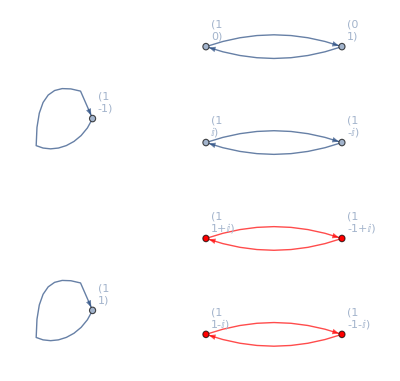
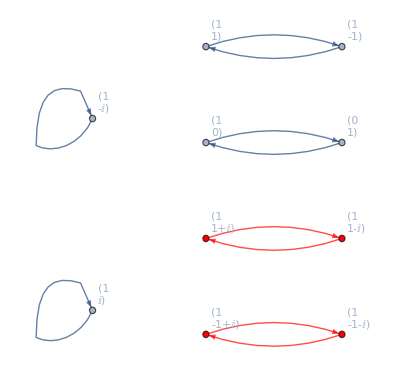
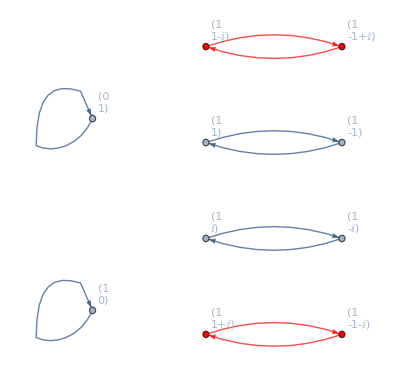
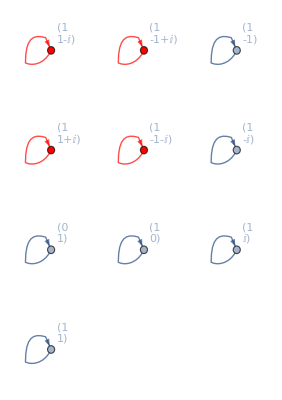

```mathematica
cGraphStates[f_,states_List,p_Integer,label_Integer:20]:=Module[{
zeroNormStates=Select[states,cNorm2[#,p]==0&],
nonZeroNormStates=Select[states,cNorm2[#,p]≠0&],
edge=DirectedEdge[#,mapToCanonical[f[#],p]]&,vertices,edges},
vertices=Join[Style[#,Red]&/@zeroNormStates,nonZeroNormStates];
edges=Join[Style[edge[#],Red]&/@zeroNormStates,edge/@nonZeroNormStates];
If[Length[states]≤label,Graph[vertices,edges,VertexLabels->(#->cMatrixForm[#]&/@states)],Graph[vertices,edges]]]
cGraphUnNormalizedStates[m_List,p_Integer,d_Integer,label_Integer:20]:=cGraphStates[cMatVecMult[m,#,p]&,testFlatten[p,d],p,label]
Print@@(cGraphUnNormalizedStates[cListForm[PauliMatrix[#]],3,2]&/@Range[4])
```

When d=2, p=3, there are 96 unitary matrices, 4 zero-norm states (except (0,0,...,0)), and 6 non-zero-norm states. These unitary matrices can be classified by the orbits they acted on both zero-norm and non-zero-norm states in the following table.

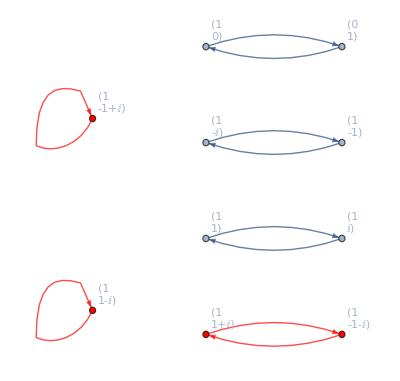
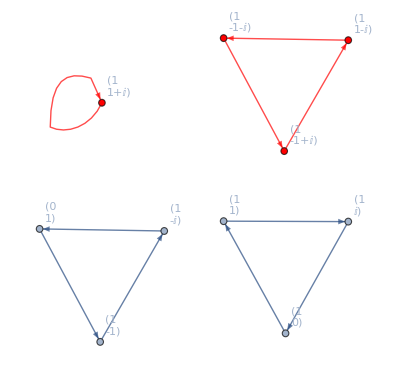
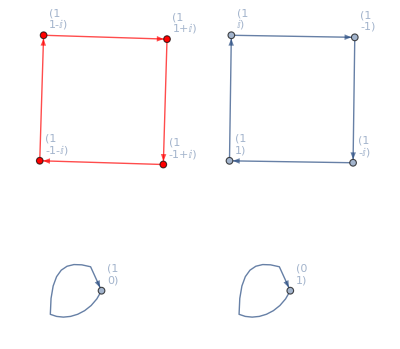
Orbits
of
States | Number
of
matrix | Example | Graph of example
4 1-cycle
in zero-norm
states;
6 1-cycle
in non-zero-norm
states. | 4 | (-1 | 0
0 | -1) | -Graphics-
2 2-cycle
in zero-norm
states;
2 1-cycle
2 2-cycle
in non-zero-norm
states. | 12 | (0 | -1
-1 | 0) | -Graphics-
2 1-cycle
1 2-cycle
in zero-norm
states;
3 2-cycle
in non-zero-norm
states. | 24 | (0 | -1
-ⅈ | 0) | -Graphics-
1 1-cycle
1 3-cycle
in zero-norm
states;
2 3-cycle
in non-zero-norm
states. | 32 | (1+ⅈ | 1-ⅈ
1+ⅈ | -1+ⅈ) | -Graphics-
1 4-cycle
in zero-norm
states;
2 1-cycle
1 4-cycle
in non-zero-norm
states. | 24 | (-1 | 0
0 | -ⅈ) | -Graphics-

When d=2, p=3, there are 96 unitary matrices, 4 zero-norm states (except (0,0,...,0)), and 6 non-zero-norm states. These unitary matrices can be classified by the orbits they acted on both zero-norm and non-zero-norm states in the following table.

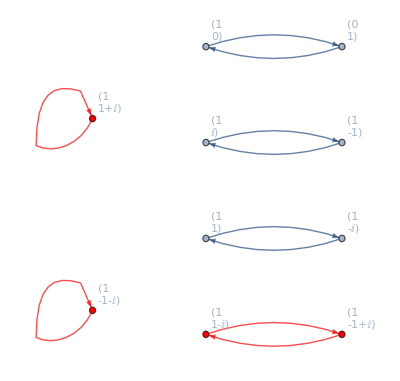
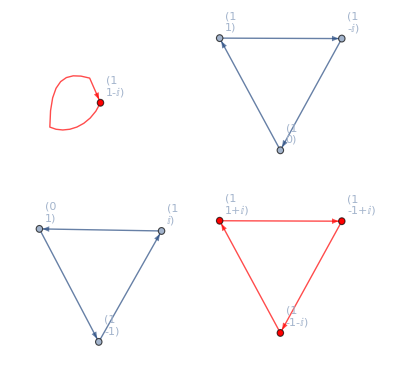
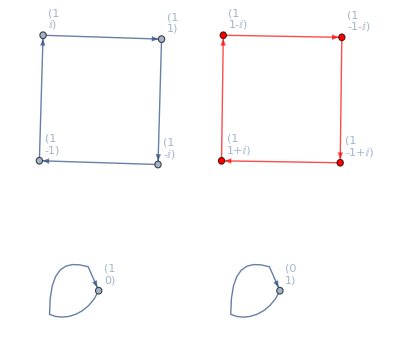
Orbits
of
States | Det | Number
of
matrix | Example | Graph of example
4 1-cycle
in zero-norm
states;
6 1-cycle
in non-zero-norm
states. | -1 | 2 | (-ⅈ | 0
0 | -ⅈ) | -Graphics-
4 1-cycle
in zero-norm
states;
6 1-cycle
in non-zero-norm
states. | 1 | 2 | (-1 | 0
0 | -1) | -Graphics-
2 2-cycle
in zero-norm
states;
2 1-cycle
2 2-cycle
in non-zero-norm
states. | -1 | 6 | (0 | -1
-1 | 0) | -Graphics-
2 2-cycle
in zero-norm
states;
2 1-cycle
2 2-cycle
in non-zero-norm
states. | 1 | 6 | (0 | -1
1 | 0) | -Graphics-
2 1-cycle
1 2-cycle
in zero-norm
states;
3 2-cycle
in non-zero-norm
states. | -ⅈ | 12 | (0 | -1
-ⅈ | 0) | -Graphics-
2 1-cycle
1 2-cycle
in zero-norm
states;
3 2-cycle
in non-zero-norm
states. | ⅈ | 12 | (0 | -1
ⅈ | 0) | -Graphics-
1 1-cycle
1 3-cycle
in zero-norm
states;
2 3-cycle
in non-zero-norm
states. | -1 | 16 | (1+ⅈ | 1-ⅈ
1+ⅈ | -1+ⅈ) | -Graphics-
1 1-cycle
1 3-cycle
in zero-norm
states;
2 3-cycle
in non-zero-norm
states. | 1 | 16 | (1+ⅈ | -1+ⅈ
1+ⅈ | 1-ⅈ) | -Graphics-
1 4-cycle
in zero-norm
states;
2 1-cycle
1 4-cycle
in non-zero-norm
states. | -ⅈ | 12 | (-1 | 0
0 | ⅈ) | -Graphics-
1 4-cycle
in zero-norm
states;
2 1-cycle
1 4-cycle
in non-zero-norm
states. | ⅈ | 12 | (-1 | 0
0 | -ⅈ) | -Graphics-

```mathematica
cClassify[Matrices_List,p_Integer,d_Integer,f_]:=SortBy[Module[{m=#⟦cArgMin[ByteCount/@cComplexForm[#]]⟧},Join[f[m],{Length[#],cMatrixForm[m],cGraphUnNormalizedStates[m,p,d]}]]&/@GatherBy[Matrices,f],Max[#⟦1,1,-1,1⟧,#⟦1,2,-1,1⟧]&]
cClassifyExplain[Matrices_List,explain_String,p_Integer,d_Integer,f_,title_List]:=Module[{cycles=Row[{#⟦2⟧," ",#⟦1⟧,"-cycle"}]&},
Print["When d=",d,", p=",p,", there are ",Length[Matrices],explain,", ",Style[cTestZeroCount[p,d],Red],Style[" zero-norm states (except (0,0,...,0))",Red],", and ",ctestExceptZeroCount[p,d]," non-zero-norm states. These",explain," can be classified by the orbits they acted on both ",Style["zero-norm",Red]," and non-zero-norm states in the following table."];
Print[Grid[Prepend[Prepend[Rest[#],Column[Join[Style[cycles[#],Red]&/@#⟦1,1⟧,{Style["in zero-norm",Red],Style["states;",Red]},cycles/@#⟦1,2⟧,{"in non-zero-norm","states."}]]]&/@cClassify[Matrices,p,d,f],Join[title,{Column[{"Number","of","matrix"}],"Example","Graph of example"}]],Dividers->{False,All}]]]
cUnitaryGroupClassifyByOrbitExplain[p_Integer,d_Integer]:=cClassifyExplain[cUnitaryGroup[p,d]," unitary matrices",p,d,{cMatrixOrbitsCountBoth[#,p]}&,{Column[{"Orbits","of","States"}]}]
cUnitaryGroupClassifyByOrbitExplain[3,2]
cUnitaryGroupClassifyByMoreExplain[p_Integer,d_Integer]:=cClassifyExplain[cUnitaryGroup[p,d]," unitary matrices",p,d,{cMatrixOrbitsCountBoth[#,p],cComplexForm[cMod[cDet[#],p]]}&,{Column[{"Orbits","of","States"}],"Det"}]
cUnitaryGroupClassifyByMoreExplain[3,2]
```

When d=2, p=3, there are 24 evolutions, 4 zero-norm states (except (0,0,...,0)), and 6 non-zero-norm states. These evolutions can be classified by the orbits they acted on both zero-norm and non-zero-norm states in the following table.

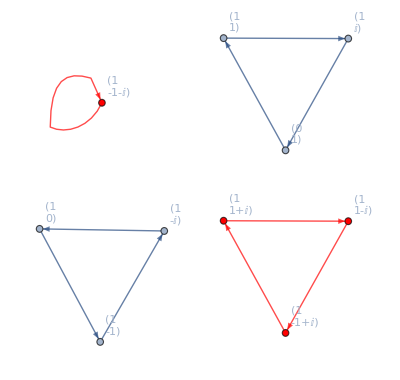
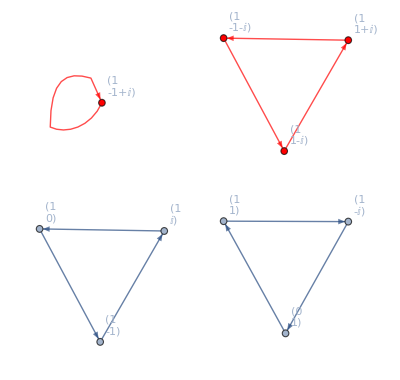
Orbits
of
States | Det | Number
of
matrix | Example | Graph of example
4 1-cycle
in zero-norm
states;
6 1-cycle
in non-zero-norm
states. | 1 | 1 | (1 | 0
0 | 1) | -Graphics-
2 2-cycle
in zero-norm
states;
2 1-cycle
2 2-cycle
in non-zero-norm
states. | -1 | 2 | (1 | 0
0 | -1) | -Graphics-
2 2-cycle
in zero-norm
states;
2 1-cycle
2 2-cycle
in non-zero-norm
states. | 1 | 1 | (0 | 1
-1 | 0) | -Graphics-
2 1-cycle
1 2-cycle
in zero-norm
states;
3 2-cycle
in non-zero-norm
states. | -ⅈ | 5 | (0 | 1
ⅈ | 0) | -Graphics-
2 1-cycle
1 2-cycle
in zero-norm
states;
3 2-cycle
in non-zero-norm
states. | ⅈ | 1 | (0 | 1
-ⅈ | 0) | -Graphics-
1 1-cycle
1 3-cycle
in zero-norm
states;
2 3-cycle
in non-zero-norm
states. | -1 | 4 | (-1-ⅈ | 1-ⅈ
1+ⅈ | 1-ⅈ) | -Graphics-
1 1-cycle
1 3-cycle
in zero-norm
states;
2 3-cycle
in non-zero-norm
states. | 1 | 4 | (-1-ⅈ | -1+ⅈ
1+ⅈ | -1+ⅈ) | -Graphics-
1 4-cycle
in zero-norm
states;
2 1-cycle
1 4-cycle
in non-zero-norm
states. | -ⅈ | 1 | (1 | 0
0 | -ⅈ) | -Graphics-
1 4-cycle
in zero-norm
states;
2 1-cycle
1 4-cycle
in non-zero-norm
states. | ⅈ | 5 | (1 | 0
0 | ⅈ) | -Graphics-

```mathematica
cEvolutionClassifyByOrbitExplain[p_Integer,d_Integer]:=cClassifyExplain[cEvolution[p,d]," evolutions",p,d,{cMatrixOrbitsCountBoth[#,p],cComplexForm[cMod[cDet[#],p]]}&,{Column[{"Orbits","of","States"}],"Det"}]
cEvolutionClassifyByOrbitExplain[3,2]
```

Timing[cUnitaryGroupClassifyByOrbitExplain[7, 2]]
FrontEndTokenExecute["Save"]

When d=2, p=7, there are 2688 unitary matrices, 8 zero-norm states (except (0,0,...,0)), and 42 non-zero-norm states. These unitary matrices can be classified by the orbits they acted on both zero-norm and non-zero-norm states in the following table.

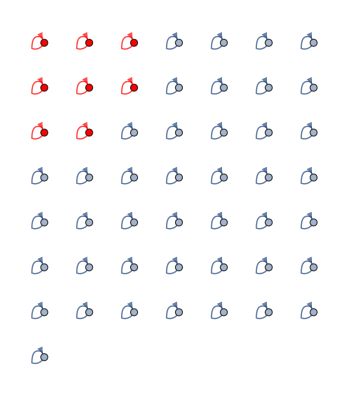
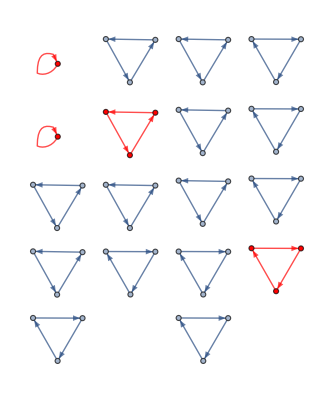
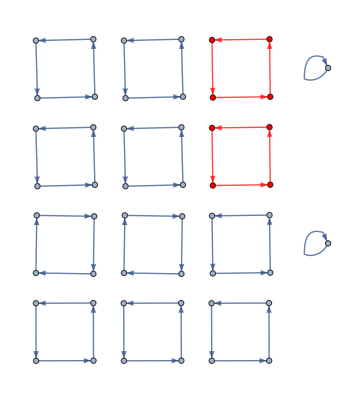
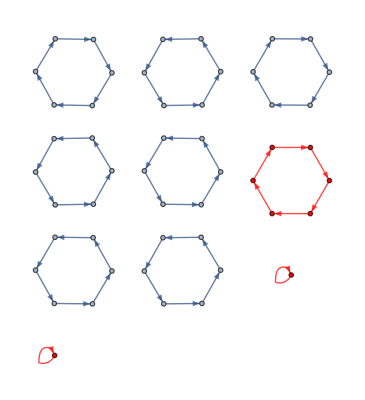
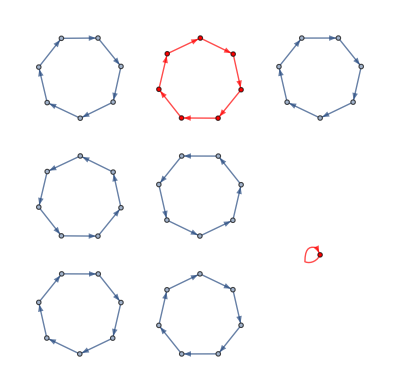
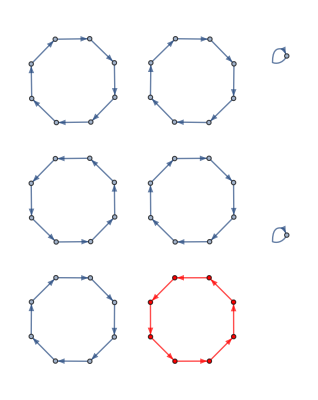
Orbits
of
States | Number
of
matrix | Example | Graph of example
8 1-cycle
in zero-norm
states;
42 1-cycle
in non-zero-norm
states. | 8 | (-1 | 0
0 | -1) | -Graphics-
4 2-cycle
in zero-norm
states;
2 1-cycle
20 2-cycle
in non-zero-norm
states. | 168 | (-2 | -2
-2 | 2) | -Graphics-
2 1-cycle
3 2-cycle
in zero-norm
states;
21 2-cycle
in non-zero-norm
states. | 224 | (0 | -2-2 ⅈ
-1 | 0) | -Graphics-
2 1-cycle
2 3-cycle
in zero-norm
states;
14 3-cycle
in non-zero-norm
states. | 448 | (-2 ⅈ | -2
-2 ⅈ | 2) | -Graphics-
2 4-cycle
in zero-norm
states;
2 1-cycle
10 4-cycle
in non-zero-norm
states. | 336 | (-2 | 2
-2 | -2) | -Graphics-
2 1-cycle
1 6-cycle
in zero-norm
states;
7 6-cycle
in non-zero-norm
states. | 448 | (-2 | -3-3 ⅈ
-2 | 3+3 ⅈ) | -Graphics-
1 1-cycle
1 7-cycle
in zero-norm
states;
6 7-cycle
in non-zero-norm
states. | 384 | (3 | -3-2 ⅈ
2+3 ⅈ | 3 ⅈ) | -Graphics-
1 8-cycle
in zero-norm
states;
2 1-cycle
5 8-cycle
in non-zero-norm
states. | 672 | (-2-2 ⅈ | 0
0 | -1) | -Graphics-

{5.60044,Null}

Timing[cUnitaryGroupClassifyByOrbitExplain[11, 2]]
FrontEndTokenExecute["Save"]

When d=2, p=11, there are 15840 unitary matrices, 12 zero-norm states (except (0,0,...,0)), and 110 non-zero-norm states. These unitary matrices can be classified by the orbits they acted on both zero-norm and non-zero-norm states in the following table.

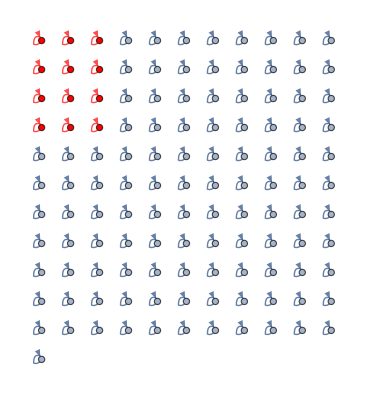
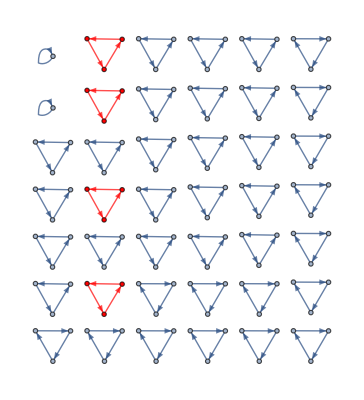
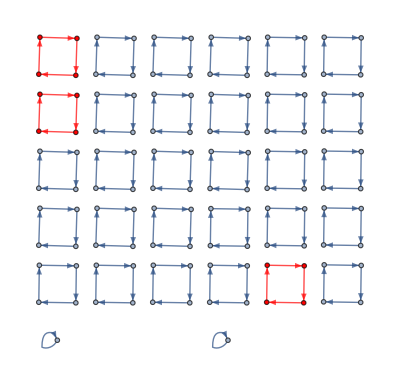
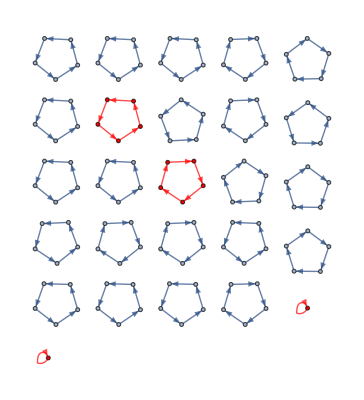
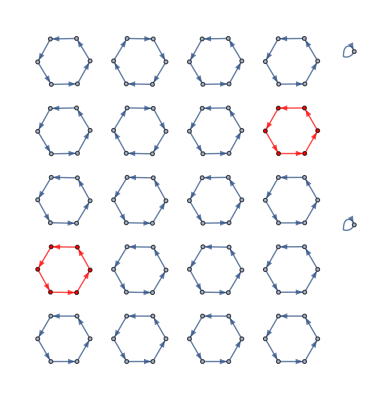
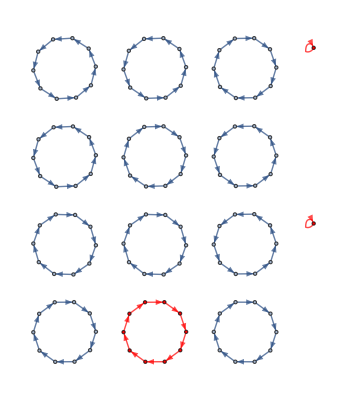
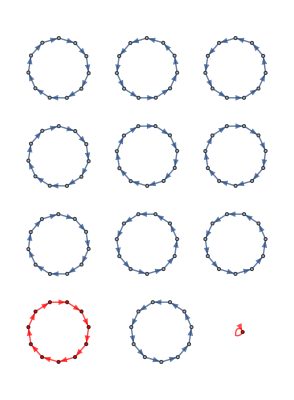
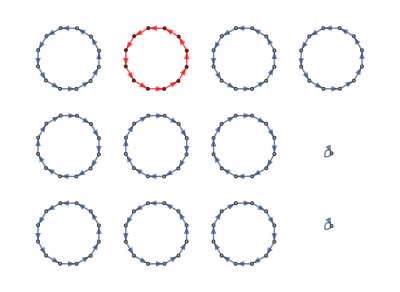
Orbits
of
States | Number
of
matrix | Example | Graph of example
12 1-cycle
in zero-norm
states;
110 1-cycle
in non-zero-norm
states. | 12 | (-1 | 0
0 | -1) | -Graphics-
6 2-cycle
in zero-norm
states;
2 1-cycle
54 2-cycle
in non-zero-norm
states. | 660 | (3 | 5
5 | -3) | -Graphics-
2 1-cycle
5 2-cycle
in zero-norm
states;
55 2-cycle
in non-zero-norm
states. | 792 | (0 | -3-5 ⅈ
-1 | 0) | -Graphics-
4 3-cycle
in zero-norm
states;
2 1-cycle
36 3-cycle
in non-zero-norm
states. | 1320 | (5 | -3
3 | 5) | -Graphics-
3 4-cycle
in zero-norm
states;
2 1-cycle
27 4-cycle
in non-zero-norm
states. | 1320 | (-1 | 0
0 | -ⅈ) | -Graphics-
2 1-cycle
2 5-cycle
in zero-norm
states;
22 5-cycle
in non-zero-norm
states. | 3168 | (3+4 ⅈ | 3
3 | -3+4 ⅈ) | -Graphics-
2 6-cycle
in zero-norm
states;
2 1-cycle
18 6-cycle
in non-zero-norm
states. | 1320 | (3 | -5
5 | 3) | -Graphics-
2 1-cycle
1 10-cycle
in zero-norm
states;
11 10-cycle
in non-zero-norm
states. | 3168 | (3 | -5
4+3 ⅈ | -2+4 ⅈ) | -Graphics-
1 1-cycle
1 11-cycle
in zero-norm
states;
10 11-cycle
in non-zero-norm
states. | 1440 | (-2+ⅈ | 5-2 ⅈ
-3+3 ⅈ | -4) | -Graphics-
1 12-cycle
in zero-norm
states;
2 1-cycle
9 12-cycle
in non-zero-norm
states. | 2640 | (-3-5 ⅈ | 0
0 | -1) | -Graphics-

{73.02407,Null}

Timing[cUnitaryGroupClassifyByOrbitExplain[3, 3]]
FrontEndTokenExecute["Save"]

When d=3, p=3, there are 24192 unitary matrices, 28 zero-norm states (except (0,0,...,0)), and 63 non-zero-norm states. These unitary matrices can be classified by the orbits they acted on both zero-norm and non-zero-norm states in the following table.

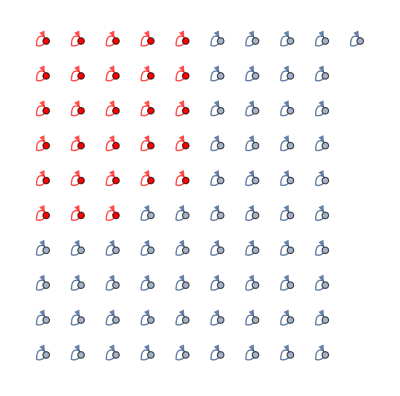
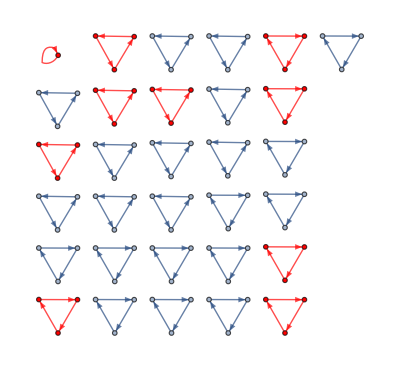
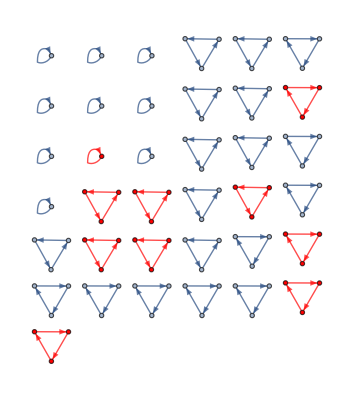
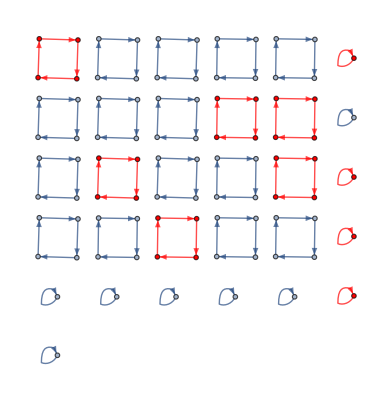
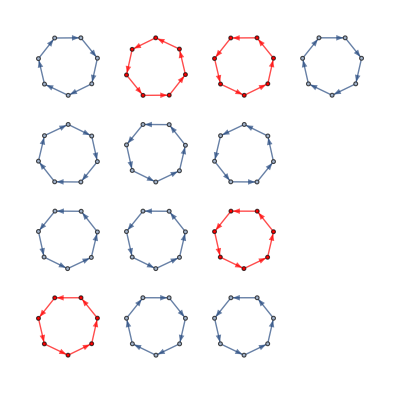
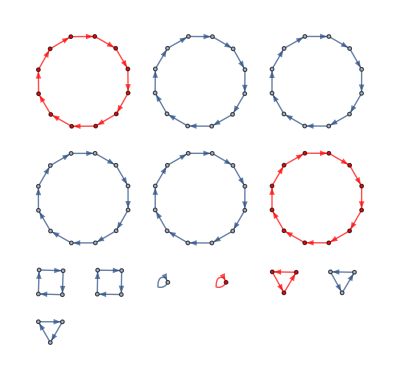
Orbits
of
States | Number
of
matrix | Example | Graph of example
28 1-cycle
in zero-norm
states;
63 1-cycle
in non-zero-norm
states. | 4 | (-1 | 0 | 0
0 | -1 | 0
0 | 0 | -1) | -Graphics-
4 1-cycle
12 2-cycle
in zero-norm
states;
7 1-cycle
28 2-cycle
in non-zero-norm
states. | 252 | (0 | 0 | -1
0 | -1 | 0
-1 | 0 | 0) | -Graphics-
1 1-cycle
9 3-cycle
in zero-norm
states;
21 3-cycle
in non-zero-norm
states. | 2688 | (0 | 0 | -1
-1 | 0 | 0
0 | -1 | 0) | -Graphics-
1 1-cycle
9 3-cycle
in zero-norm
states;
9 1-cycle
18 3-cycle
in non-zero-norm
states. | 224 | (1+ⅈ | -1 | -1
-1 | 1+ⅈ | 1
-1 | 1 | 1+ⅈ) | -Graphics-
4 1-cycle
6 4-cycle
in zero-norm
states;
7 1-cycle
14 4-cycle
in non-zero-norm
states. | 504 | (-1 | 0 | 0
0 | -1 | 0
0 | 0 | -ⅈ) | -Graphics-
2 2-cycle
6 4-cycle
in zero-norm
states;
3 1-cycle
2 2-cycle
14 4-cycle
in non-zero-norm
states. | 1512 | (0 | 0 | -1
0 | -1 | 0
1 | 0 | 0) | -Graphics-
1 1-cycle
1 3-cycle
4 6-cycle
in zero-norm
states;
1 1-cycle
4 2-cycle
2 3-cycle
8 6-cycle
in non-zero-norm
states. | 2016 | (1+ⅈ | -1 | -1
-1 | 1 | 1+ⅈ
-1 | 1+ⅈ | 1) | -Graphics-
4 7-cycle
in zero-norm
states;
9 7-cycle
in non-zero-norm
states. | 6912 | (1+ⅈ | 1 | -1
-1 | -1 | 1+ⅈ
-1 | -1-ⅈ | 1) | -Graphics-
2 1-cycle
1 2-cycle
3 8-cycle
in zero-norm
states;
1 1-cycle
3 2-cycle
7 8-cycle
in non-zero-norm
states. | 6048 | (0 | 0 | -1
0 | -1 | 0
-ⅈ | 0 | 0) | -Graphics-
1 1-cycle
1 3-cycle
2 12-cycle
in zero-norm
states;
1 1-cycle
2 3-cycle
2 4-cycle
4 12-cycle
in non-zero-norm
states. | 4032 | (1+ⅈ | 1 | 1
-1 | -1 | -1-ⅈ
-1 | -1-ⅈ | -1) | -Graphics-

{104.61427,Null}

```mathematica
zeroNormStatesCount[p_Integer,d_Integer]:=p^(d-1)(p^d+(-1)^d(p-1))-1
zeroNormStatesCount[#,2]&/@{3,7,11}
zeroNormStatesCount[3,3]
```

{32,384,1440}

224

```mathematica
imCount[p_Integer]:=Length[Select[cBasis[p],#≠{0,0}∧#+cConj[#]=={0,0}&]]
imCount/@{3,7,11}
```

{2,6,10}

```mathematica
transvectionCount[p_Integer,d_Integer]:=(zeroNormStatesCount[p,d] imCount[p])/(p-1)
transvectionCount[#,2]&/@{3,7,11}
transvectionCount[3,3]
```

{32,384,1440}

224